## Problema de valor de contorno de Dirichelet 1D

### Dados de entrada

```mathematica
degree=1;            (* Grau do elemento *)
Nelem=64;            (* Número de elementos *)
```

### Dados do problema

```mathematica
k[x_]:=1                              (* módulo do material*)
c[x_]:=0                               (*coeficiente da primeira derivada da variável de estado*)
b[x_]:=1                                 (*coeficiente da variável de estado*)

Xini=0;
Xfin=1;
h=Abs[Xini-Xfin]/Nelem;        (* Tamanho do elemento *)
dx=h/degree;                                     (* Partição do dominínio *)

(*UExata[x_]=(x)-Sinh[x]/Sinh[1];
f[x_]=Simplify[-k[x]*D[UExata[x],{x,2}]+c[x]*D[UExata[x],x]+b[x]*UExata[x]];
U0=UExata[Xini];
UL=UExata[Xfin];*)

(* FUNCIONAL *)
U0=0;                                                      (* C.C. Dirichlet em x = Xini *)
UL=0;                                                      (* C.C. Dirichlet em x = Xfin *)

f[x_]= 1;          (* Fonte *)
fPontual[x_,XNode_]=10*DiracDelta[x-XNode] ;
UExata[x_]=Flatten[DSolve[{-k[x]D[uu[x],{x,2}]+c[x]*D[uu[x],x]+b[x]*uu[x]==f[x],uu[Xini]==U0,uu[Xfin]==UL},uu[x],x]] [[1,2]];
```

### Construção das funções de forma

```mathematica
coef=ToExpression[Table[FromCharacterCode[{97+i,97+i}],{i,0,degree}]];     (* coeficientes do polinômio a ser formado*)

Pol[ξ_]=Sum[coef[[k+1]]*ξ^(k ),{k,0,degree} ];                                                                                                  (* Polinômio genérico *)

Ncoef=Flatten[Table[NSolve[Table[Pol[j/degree]==KroneckerDelta[j-i],{j,0,degree}],coef],{i,0,degree}],1];

PhiQsi=Table[Pol[ξ]/.Ncoef[[i]],{i,1,degree+1}];

ω0=Xini;
ω1=ω0+h;
Subst=1/(ω1-ω0)*(x-ω0);                              
Phi=PhiQsi/.ξ-> Subst;          (* Phi local no domiínio *)
DerPhi=D[Phi,x];
```

### Matriz de Rigidez e Vetor de carga para um elemento Genérico

```mathematica
KLoc=Table[0,{degree+1},{degree+1}];

For[i=1,i<=degree+1,i++,
      
 For[j=1,j<=degree+1,j++,
                 
 KLoc[[i,j]]=Integrate[(k[x]*DerPhi[[i]]*DerPhi[[j]]+c[x]*DerPhi[[j]]*Phi[[i]]+b[x]*Phi[[i]]*Phi[[j]]),{x,ω0,ω1}] ; 
   
      ];
   ];
KLoc//MatrixForm;
```

### Assemblagem

```mathematica
K=Table[0,{i,Nelem*degree+1},{j,Nelem*degree+1}];
F=Table[0,{Nelem*degree+1}];

(*  ======= Global Computing (Assembling) =======  *)
For[el = 1, el ≤ Nelem,

	For[  px=1, px≤ degree+1,px++,

		   For[       py=1,py≤ degree+1,py++,

		   	     K[[(el-1)*degree+px,(el-1)*degree+py]]+=KLoc[[px,py]];
	                 ];
 PhiTemp=Phi/.x->(x-(el-1)*h);

Floc=Table[Integrate[f[x]*PhiTemp[[i]],{ x, ω0 +(el-1)*h, ω1 + (el-1)*h } ],{i,1,degree+1}];
 
F[[(el-1)*degree+px]]+=Floc[[px]];
             
 ];
         
 el++];

K//MatrixForm;
F//MatrixForm;

(* ==== Compensar as condiçoões de contorno === *)
 For[  i=1,i≤Nelem*degree+1,i++,
	
K[[1,i]]=0;
	
K[[Nelem*degree+1,i]]=0;
    ];

K[[1,1]]=1;K[[Nelem*degree+1,Nelem*degree+1]]=1;
F[[1]]=U0;
F[[Nelem*degree+1]]=UL;
```

### Resolver sistema

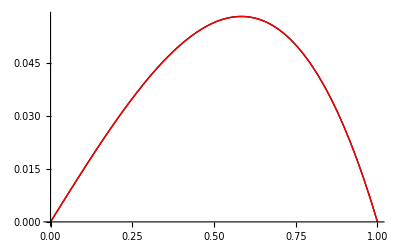

```mathematica
(* Solving Linear System *)
α=LinearSolve[N[K],N[F]];

(* Computing the Nodal Polinomials for All the Domain *)

Phi[[1]]=Piecewise[{{Phi[[degree+1]]/.x->(x+h), (ω0-h)≤ x ≤ω0},{Phi[[1]],ω0≤ x≤  ω1}}];

Phi[[degree+1]]=Piecewise[{{Phi[[degree+1]],ω0≤ x≤ω1},{Phi[[1]]/.x->(x-h),ω1≤  x≤  (ω1+h)}}];

For[   i=2,i≤degree,i++,
	
Phi[[i]]=Piecewise[{{Phi[[i]],ω0≤x≤ ω1}}];

];

Fi=Table[0,{degree*Nelem+1}];

For[   i=1,i≤degree*Nelem+1,i++,
	
Index=Round[(dx*(i-1)-Quotient[dx*(i-1),h]*h)/dx]+1;
	
Fi[[i]]=Phi[[Index]]/.{x->(x-Quotient[dx*(i-1),h]*h)};
];
Un=Chop[α.Fi];
PlotAprox=Plot[Un,{x,Xini,Xfin}, PlotStyle-> {Red},PlotLabel-> "Solução Aproximada"];
Needs["PlotLegends`"];
Graf2=Plot[{UExata[x],Un},{x,Xini,Xfin}, PlotStyle-> {Black,Red},PlotLegend-> {"Sol. Primal","Sol. Aproximada"},LegendPosition-> {0.9,0}(*,LegendSize->.6*),LegendTextSpace->7]
```

```mathematica
Export["DualP2NEl16.eps",Graf1]
```

DualP2NEl16.eps

### Calculo do erro nas Normas H1, Semi-H1, L2 e Energia

```mathematica
Erro=UExata[x]-PiecewiseExpand[Un];

Energia=Integrate[k[x]*D[Erro,x]*D[Erro,x]+c[x]*D[Erro,x]*Erro+b[x]*Erro*Erro,{x,Xini,Xfin}];
NormaEnergia=Sqrt[Energia];
Print[" ErroEn  = ",N[ NormaEnergia]];

(*NormaSH1=Sqrt[Integrate[D[Erro,x]^2,{x,Xini,Xfin}]];
Print[" ErroSH1  = ",N[ NormaSH1]];

NormaH1=Sqrt[Integrate[D[Erro,x]^2+Erro^2,{x,0,1}]];*)
(*Print[" ErroH1  = ",N[ NormaH1]];*)

L2=Integrate[Erro*Erro,{x,Xini,Xfin}];
NormaL2=Sqrt[L2];
Print[" ErroL2  = ",N[ NormaL2]];
```

ErroEn  = 0.000038138

ErroL2  = 3.67507×10^-7

### Erro no Funcional Linear Limitado

```mathematica
R[var_]:=Piecewise[{{1,0.50≤ var≤0.75} } ]
L[Sol_,var_]:=Integrate[Sol,{var,Xini,Xfin}]
Abs[L[UExata[x],x]-L[Un,x]]
```

1.95688×10^-12

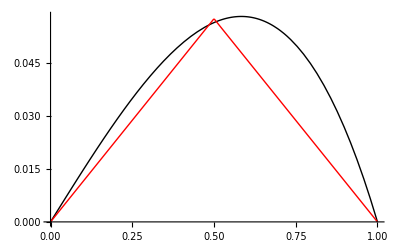

```mathematica
A=Graf1
```

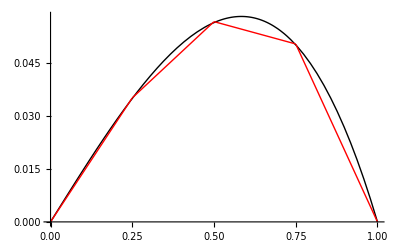

```mathematica
B=Graf2
```